为对象指派名称

使用 % 来引用你最近的计算结果往往很方便，特别是当你想在 Wolfram 语言中进行快速实验时。

进行一个简单的计算：

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

% 将给出上一次计算的结果：

```mathematica
%
```

{1,2,3,4,5,6,7,8,9,10}

这将计算最近的结果的平方：

```mathematica
%^2
```

{1,4,9,16,25,36,49,64,81,100}

如果你希望后面再引用结果，可以给它指定一个名字。例如，你可以说 thing=Range[10] 来指定 thing 作为 Range[10] 的结果的名称。

将 thing 指派为 Range[10] 的结果的名称：

```mathematica
thing=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

每当 thing 出现时，它就会被 Range[10] 的结果所取代：

```mathematica
thing
```

{1,2,3,4,5,6,7,8,9,10}

计算 thing 的值的平方：

```mathematica
thing^2
```

{1,4,9,16,25,36,49,64,81,100}

你可以给计算的结果指定一个名字，即使你从未将结果进行显示。用 ; (分号)来结束输入，可以避免看到结果。

为一个包含一百万个元素的列表指定一个名字，但不显示这个列表：

```mathematica
millionlist=Range[1000000];
```

找到列表中所有元素的总和：

```mathematica
Total[millionlist]
```

500000500000

当你给某个对象指定一个名字时，这个名字会一直存在，直到你明确地清除它。

将 x 赋值为 42：

```mathematica
x=42
```

42

你可能认为结果是 {x,y,z}，但 x 的值为 42：

```mathematica
{x,y,z}
```

{42,y,z}

如果你想清除赋值，请使用 Clear：

清除 x 的所有赋值：

```mathematica
Clear[x]
```

现在，x 就像 y 和 z 一样，没有被替换：

```mathematica
{x,y,z}
```

{x,y,z}

为 x 指定一个全局值，比如 x=42，有可能是个大问题，因为它可能影响你在会话中进行的一切(至少在你清除 x 之前)。更安全并且非常有用的方法是在一个模块中为 x 指派一个临时的、局部的值。

这将在  Module 内将 x 的值局部设置为 Range[10]：

```mathematica
Module[{x=Range[10]},x^2]
```

{1,4,9,16,25,36,49,64,81,100}

在模块外，x 仍然没有被赋值：

```mathematica
x
```

x

你可以在一个模块内有任意多的局部变量。

定义局部变量 x 和 n，然后用你指派的值来计算 x^n：

```mathematica
Module[{x=Range[10],n=2},x^n]
```

{1,4,9,16,25,36,49,64,81,100}

在本书大部分内容中使用的函数式编程中，你通过应用一系列函数来执行一系列操作。这是一种非常强大和直接的编程方式，也是 Wolfram 语言的独特之处。

但是一旦定义了变量，就可以使用另一种风格，即不直接将结果从一个函数送入另一个函数，而是将它们指派为变量的值，以便以后使用。这种程序化编程是自早期计算时代起就在低级语言中使用的。

它在 Wolfram 语言中仍然很有用，尽管在许多方面与函数式编程以及我们后面将讨论的基于模式的编程风格相比有所失色。

要在 Wolfram 语言中指定一系列操作，只需用分号(;)将它们分隔开。(把分号放在最后，就像指定了一个空的最后动作，这就是为什么这能让结果不显示)。

进行一系列的操作；最终的结果是最后一个操作生成的结果：

```mathematica
x=Range[10];y=x^2;y=y+10000
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

上述操作会定义 x 和 y 的全局值；别忘了清除它们：

```mathematica
Clear[x,y]
```

你可以在 Module 内使用分号来进行一系列操作。

这将进行一系列操作，并且 x 和 y 都是作为局部变量：

```mathematica
Module[{x,y},x=Range[10];y=x^2;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

你可以混合使用有和没有初始值的局部变量：

```mathematica
Module[{x,y,n=2},x=Range[10];y=x^n;y=y+10000]
```

{10001,10004,10009,10016,10025,10036,10049,10064,10081,10100}

你可以嵌套模块，如果你正在构建大型程序，你想隔开代码的不同部分，这很有用。

词汇

% |   | 最近的计算结果
x=value |   | 赋值
Clear[x] |   | 清除值
Module[{x=value}, ...] |   | 创建一个临时变量
expr; |   | 进行计算，但不显示计算结果
expr_1;  expr_2;  ... |   | 进行一系列计算

"共有 7 道习题" | "开始练习 »"

使用 Module 来计算 x^2+x，其中 x 为 Range[10]。»

| 期望输出： |  
  | {2,6,12,20,30,42,56,72,90,110} |

使用 Module 来生成包含 10 个 100 以内的随机整数的列表，然后创建一个列，依次给出原始列表，应用 Sort、Max 以及 Total 后的结果。»

| 期望输出示例： |  
  | {38,25,79,92,19,68,53,39,71,2}
{2,19,25,38,39,53,68,71,79,92}
92
486 |

使用 Module 来生成一个图像拼贴画，图片依次为一张长颈鹿的图片，对其应用 Blur、EdgeDetect 以及 ColorNegate 的结果。»

| 期望输出示例： |  
  | -Graphics- |

在 Module 内，让 r=Range[10]，然后将 r 与反向的 r、r、反向的 r 依次进行连接，最后将连接结果绘制为线条图。»

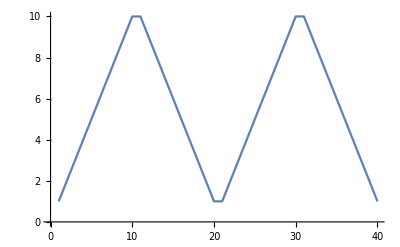
| 期望输出： |  
  | -Graphics- |

为 {Range[10]+1,Range[10]-1,Reverse[Range[10]]} 找到一个更简单的形式。»

| 期望输出： |  
  | {{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}} |

为 Module[{u=10},Join[{u},Table[u=Mod[17u+2,11],20]]] 找到一个更简单的形式。»

| 期望输出： |  
  | {10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10} |

生成 10 个由 5 个字母组成的随机字符串，其中辅音(非元音)字母与元音(aeiou)字母交替出现。»

| 期望输出示例： |  
  | {"nafam","toqay","xuheq","hawop","wiyoj","vozop","sasek","dabaw","xicap","yayok"} |

问&答

怎么会到了第 38 节才开始引入变量赋值？

因为，正如我们所看到的，在 Wolfram 语言中，即使不进行变量赋值，我们也可以进行得很深入。而且，没有这些东西，程序就会变得更干净。

我可以为任何对象指派名字吗？

是的。图形、数组、图像、纯函数，什么都可以。

如何读 x=4？

“x 等于 4”，或者，用的更少一点，“将 x 指派给 4”，或者“给定 x 值为 4”。

关于全局名称有哪些好的原则？

使用具体而明确的名称。不要担心它们太长；当你输入时，它们会被自动完成。对于“非正式”的名字，以小写字母为起始。对于更深思熟虑的名字，考虑使用大写字母，就像内置函数那样。

% 将给出上一个结果，那上上个结果呢？

%% 将给出上上个结果，%%% 将给出上上上个结果，以此类推。%n 将给出第 n 行的结果，也就是时标记为 Out[n] 的结果。

我可以同时给多个变量赋值吗？

是的。x=y=6 将把 x 和 y 都赋值为 6。{x,y}={3,4} 将把 x 赋值为 3，y 赋值为 4。 {x,y}={y,x} 将交换 x 和 y 的值。

如果一个变量在没有被赋值的情况下从模块中逃逸，会发生什么？

尽管试试吧！你会发现你将得到一个新的变量，它被指派了一个唯一的名字。

其他程序化编程结构，比如 Do 和 For 呢？

Wolfram 语言包含这些。Do 有时是值得使用的，特别是当你的目标是“副作用”，比如分配变量或导出数据。For 基本上总是一个坏主意，而且几乎总是可以通过使用诸如 Table 这样的结构来创建更干净的代码。

技术笔记

x=2+2 的结果就是 4，但还为一个副作用，对 x 进行了赋值。

在纯函数式编程中，任何计算的唯一作用就是给出结果。但只要你在赋值，实际上就有一个由这些赋值设置的隐藏状态。

x=. 是 Clear[x] 的另一种形式。

Module 做的是词法范围限定，这意味着它能有效地将变量名局部化。Block 做的是动态范围限定，这意味着它对变量的值进行局部化，而不是名称。两者在不同情况下都很有用。Table 有效地使用了 Block。

x++ 与 x=x+1 等同，x+=n 与 x=x+n 等同。AppendTo[x,n] 与 x=Append[x,n] 或者 x=Join[x,{n}] 等同。